# Relationship between x and y according to different original angleß and area A

In axises, x≥ 0&&x≤ 1,y≥0&&y≤1. make robots move with an angle, they will eventually reach the edge or corner in different ship depending on the angle. they final shape of the robots can be classified to triangle, and right trapezoid. Both in triangle and trapezoid shape have 4 special position whose shape is rectangle.

## Triangle

### when 0<A≤ 1/2

Rectangle

## when θ = 0

```mathematica
θ=ß;
```

```mathematica
xmean=Simplify[(∫_(1-A)^1 ∫_0^1 xⅆyⅆx)/A]
```

1-A/2

```mathematica
ymean=Simplify[(∫_0^1 ∫_(1-A)^1 yⅆxⅆy)/A]
```

1/2

```mathematica
varx=Simplify[(∫_(1-A)^1 ∫_0^1 x^2ⅆyⅆx)/A-(xmean)^2]
```

A^2/12

```mathematica
vary=Simplify[(∫_0^1 ∫_(1-A)^1 y^2ⅆxⅆy)/A-(ymean)^2]
```

1/12

```mathematica
covxy=Simplify[(∫_0^1 ∫_(1-A)^1 (x-xmean)*(y-ymean)ⅆxⅆy)/A]
```

0

```mathematica
corxy=covxy/(Sqrt[varx]*Sqrt[vary])
```

0

## when θ = π/2

```mathematica
xmean=Simplify[(∫_0^1 ∫_(1-A)^1 xⅆyⅆx)/A]
```

1/2

```mathematica
ymean=Simplify[(∫_(1-A)^1 ∫_0^1 yⅆxⅆy)/A]
```

1-A/2

```mathematica
varx=Simplify[(∫_0^1 ∫_(1-A)^1 x^2ⅆyⅆx)/A-(xmean)^2]
```

-2/3+A-A^2/4

```mathematica
vary=Simplify[(∫_(1-A)^1 ∫_0^1 y^2ⅆxⅆy)/A-(ymean)^2]
```

1/12 (3-2 A)^2

```mathematica
covxy=Simplify[(∫_(1-A)^1 ∫_0^1 (x-xmean)*(y-ymean)ⅆxⅆy)/A]
```

0

```mathematica
corxy=covxy/(Sqrt[varx]*Sqrt[vary])
```

0

## when θ = π

```mathematica
xmean=Simplify[(∫_0^A ∫_0^1 xⅆyⅆx)/A]
```

A/2

```mathematica
ymean=Simplify[(∫_0^1 ∫_0^A yⅆxⅆy)/A]
```

1/2

```mathematica
varx=Simplify[(∫_0^A ∫_0^1 x^2ⅆyⅆx)/A-(xmean)^2]
```

-1+A+A^2/12

```mathematica
vary=Simplify[(∫_0^A ∫_0^1 y^2ⅆxⅆy)/A-(ymean)^2]
```

-1/4+A^2/3

```mathematica
covxy=Simplify[(∫_0^1 ∫_0^A (x-xmean)*(y-ymean)ⅆxⅆy)/A]
```

0

```mathematica
corxy=covxy/(Sqrt[varx]*Sqrt[vary])
```

0

## when θ = (3π)/2

```mathematica
xmean=Simplify[(∫_0^1 ∫_0^A xⅆyⅆx)/A]
```

1/2

```mathematica
ymean=Simplify[(∫_0^A ∫_0^1 yⅆxⅆy)/A]
```

A/2

```mathematica
varx=Simplify[(∫_0^1 ∫_0^A x^2ⅆyⅆx)/A-(xmean)^2]
```

-2/3+A-A^2/4

```mathematica
vary=Simplify[(∫_0^A ∫_0^1 y^2ⅆxⅆy)/A-(ymean)^2]
```

-1/4+A^2/3

```mathematica
covxy=Simplify[(∫_0^A ∫_0^1 (x-xmean)*(y-ymean)ⅆxⅆy)/A]
```

0

```mathematica
corxy=covxy/(Sqrt[varx]*Sqrt[vary])
```

0

Triangle

## when 0<ß<π/2

```mathematica
θ=ß;
```

```mathematica
xmean=Simplify[(∫_(1-Sqrt[2*A*Cot[θ]])^1 (∫_(1-Tan[θ]*(y-1+Sqrt[2*A*Cot[θ]]))^1 xⅆx)ⅆy)/A]
```

1-1/3 √2 √(A Cot[ß]) Tan[ß]

```mathematica
ymean=Simplify[(∫_(1-Sqrt[2*A*Cot[θ]])^1 (∫_(1-Tan[θ]*(y-1+Sqrt[2*A*Cot[θ]]))^1 yⅆx)ⅆy)/A]
```

1-1/3 √2 √(A Cot[ß])

```mathematica
varx=Simplify[(∫_(1-Sqrt[2*A*Cot[θ]])^1 (∫_(1-Tan[θ]*(y-1+Sqrt[2*A*Cot[θ]]))^1 x^2ⅆx)ⅆy)/A-xmean^2]
```

1/9 A Tan[ß]

```mathematica
vary=Simplify[(∫_(1-Sqrt[2*A*Cot[θ]])^1 (∫_(1-Tan[θ]*(y-1+Sqrt[2*A*Cot[θ]]))^1 y^2ⅆx)ⅆy)/A-ymean^2]
```

1/9 A Cot[ß]

```mathematica
covxy=Simplify[(∫_(1-Sqrt[2*A*Cot[θ]])^1 (∫_(1-Tan[θ]*(y-1+Sqrt[2*A*Cot[θ]]))^1 x*yⅆx)ⅆy)/A-xmean*ymean]
```

ConditionalExpression[-A/18,Re[Cot[ß]/(√(A Cot[ß]))]>1/(√2)||Re[Cot[ß]/(√(A Cot[ß]))]<0||Cot[ß]/(√(A Cot[ß]))∉Reals]

```mathematica
corxy=FullSimplify[covxy/(Sqrt[varx]*Sqrt[vary])]
```

ConditionalExpression[-A/(2 √(A Cot[ß]) √(A Tan[ß])),Re[Cot[ß]/(√(A Cot[ß]))]>1/(√2)||Re[Cot[ß]/(√(A Cot[ß]))]<0||Cot[ß]/(√(A Cot[ß]))∉Reals]

## when π/2<ß<π

```mathematica
θ=ß-π/2;
```

```mathematica
xmean=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-x))^1 xⅆy)ⅆx)/A]
```

1/3 √2 √(-A Tan[ß])

```mathematica
ymean=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-x))^1 yⅆy)ⅆx)/A]
```

1+1/3 √2 Cot[ß] √(-A Tan[ß])

```mathematica
varx=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-x))^1 x^2ⅆy)ⅆx)/A-xmean^2]
```

-1/9 A Tan[ß]

```mathematica
vary=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-x))^1 y^2ⅆy)ⅆx)/A-ymean^2]
```

-1/9 A Cot[ß]

```mathematica
covxy=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-x))^1 x*yⅆy)ⅆx)/A-xmean*ymean]
```

A/18

```mathematica
corxy=FullSimplify[covxy/(Sqrt[varx]*Sqrt[vary])]
```

A/(2 √(-A Cot[ß]) √(-A Tan[ß]))

## when π<ß< (3π)/2

```mathematica
θ=ß-π;
```

```mathematica
xmean=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_0^(Tan[θ]*(Sqrt[2*A*Cot[θ]]-x)) xⅆy)ⅆx)/A]
```

1/3 √2 √(A Cot[ß])

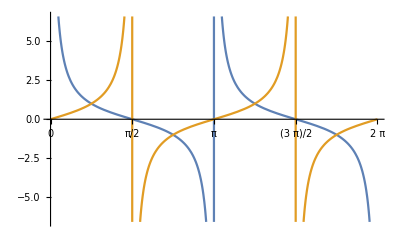

```mathematica
Plot[{Cot[β],Tan[β]},{β,0,2π},Ticks->{{0,π/2,π,3/2π,2π},Automatic}]
```

```mathematica
Clear[A,β,x,y]
```

```mathematica
xmean=Simplify[(∫_0^Sqrt[2*A*Cot[ß]] (∫_0^(Tan[ß]*(Sqrt[2*A*Cot[ß]]-x)) xⅆy)ⅆx)/A]
```

1/3 √2 √(A Cot[ß])

```mathematica
ymean=Simplify[Assuming[π<ß< (3π)/2 ,(∫_0^Sqrt[2*A*Cot[ß]] (∫_0^(Tan[ß]*(Sqrt[2*A*Cot[ß]]-x)) yⅆy)ⅆx)/A]]
```

1/3 √2 √(A Cot[ß]) Tan[ß]

```mathematica
varx=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_0^(Tan[θ]*(Sqrt[2*A*Cot[θ]]-x)) (x^2)ⅆy)ⅆx)/A-xmean^2]
```

1/9 A Cot[ß]

```mathematica
vary=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_0^(Tan[θ]*(Sqrt[2*A*Cot[θ]]-x)) (y^2)ⅆy)ⅆx)/A-ymean^2]
```

1/9 A Tan[ß]

```mathematica
covxy=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_0^(Tan[θ]*(Sqrt[2*A*Cot[θ]]-x)) (x*y)ⅆy)ⅆx)/A-xmean*ymean]
```

-A/18

```mathematica
corxy=FullSimplify[covxy/(Sqrt[varx]*Sqrt[vary])]
```

-A/(2 √(A Cot[ß]) √(A Tan[ß]))

## when (3π)/2 <ß<2π

```mathematica
θ=2π-ß;
```

```mathematica
xmean=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-y))^1 xⅆx)ⅆy)/A]
```

1+1/3 √2 √(-A Cot[ß]) Tan[ß]

```mathematica
ymean=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-y))^1 yⅆx)ⅆy)/A]
```

1/3 √2 √(-A Cot[ß])

```mathematica
varx=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-y))^1 x^2ⅆx)ⅆy)/A-xmean^2]
```

-1/9 A Tan[ß]

```mathematica
vary=Simplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-y))^1 y^2ⅆx)ⅆy)/A-ymean^2]
```

-1/9 A Cot[ß]

```mathematica
covxy=FullSimplify[(∫_0^Sqrt[2*A*Cot[θ]] (∫_(1-Tan[θ]*(Sqrt[2*A*Cot[θ]]-y))^1 x*yⅆx)ⅆy)/A-xmean*ymean]
```

A/18

```mathematica
corxy=FullSimplify[covxy/(Sqrt[varx]*Sqrt[vary])]
```

A/(2 √(-A Cot[ß]) √(-A Tan[ß]))

## Trapezoid

### when 1/2<A≤ 1

Rectangle

## when θ = 0

```mathematica
θ=ß;
```

```mathematica
xmean=Simplify[(∫_(1-A)^1 ∫_0^1 xⅆyⅆx)/A]
```

1-A/2

```mathematica
ymean=Simplify[(∫_0^1 ∫_(1-A)^1 yⅆxⅆy)/A]
```

1/2

```mathematica
varx=Simplify[(∫_(1-A)^1 ∫_0^1 x^2ⅆyⅆx)/A-(xmean)^2]
```

A^2/12

```mathematica
vary=Simplify[(∫_0^1 ∫_(1-A)^1 y^2ⅆxⅆy)/A-(ymean)^2]
```

1/12

```mathematica
covxy=Simplify[(∫_0^1 ∫_(1-A)^1 (x-xmean)*(y-ymean)ⅆxⅆy)/A]
```

0

```mathematica
corxy=covxy/(Sqrt[varx]*Sqrt[vary])
```

0

## when θ = π/2

```mathematica
xmean=Simplify[(∫_0^1 ∫_(1-A)^1 xⅆyⅆx)/A]
```

1/2

```mathematica
ymean=Simplify[(∫_(1-A)^1 ∫_0^1 yⅆxⅆy)/A]
```

1-A/2

```mathematica
varx=Simplify[(∫_0^1 ∫_(1-A)^1 x^2ⅆyⅆx)/A-(xmean)^2]
```

-2/3+A-A^2/4

```mathematica
vary=Simplify[(∫_(1-A)^1 ∫_0^1 y^2ⅆxⅆy)/A-(ymean)^2]
```

1/12 (3-2 A)^2

```mathematica
covxy=Simplify[(∫_(1-A)^1 ∫_0^1 (x-xmean)*(y-ymean)ⅆxⅆy)/A]
```

0

```mathematica
corxy=covxy/(Sqrt[varx]*Sqrt[vary])
```

0

## when θ = π

```mathematica
xmean=Simplify[(∫_0^A ∫_0^1 xⅆyⅆx)/A]
```

A/2

```mathematica
ymean=Simplify[(∫_0^1 ∫_0^A yⅆxⅆy)/A]
```

1/2

```mathematica
varx=Simplify[(∫_0^A ∫_0^1 x^2ⅆyⅆx)/A-(xmean)^2]
```

-1+A+A^2/12

```mathematica
vary=Simplify[(∫_0^A ∫_0^1 y^2ⅆxⅆy)/A-(ymean)^2]
```

-1/4+A^2/3

```mathematica
covxy=Simplify[(∫_0^1 ∫_0^A (x-xmean)*(y-ymean)ⅆxⅆy)/A]
```

0

```mathematica
corxy=covxy/(Sqrt[varx]*Sqrt[vary])
```

0

## when θ = (3π)/2

```mathematica
xmean=Simplify[(∫_0^1 ∫_0^A xⅆyⅆx)/A]
```

1/2

```mathematica
ymean=Simplify[(∫_0^A ∫_0^1 yⅆxⅆy)/A]
```

A/2

```mathematica
varx=Simplify[(∫_0^1 ∫_0^A x^2ⅆyⅆx)/A-(xmean)^2]
```

-2/3+A-A^2/4

```mathematica
vary=Simplify[(∫_0^A ∫_0^1 y^2ⅆxⅆy)/A-(ymean)^2]
```

-1/4+A^2/3

```mathematica
covxy=Simplify[(∫_0^A ∫_0^1 (x-xmean)*(y-ymean)ⅆxⅆy)/A]
```

0

```mathematica
corxy=covxy/(Sqrt[varx]*Sqrt[vary])
```

0

Trapezoid

## when 0<ß<π/2

```mathematica
θ=ß;
```

```mathematica
xmean=Simplify[(∫_0^1 ∫_(1-(A-1/2 Tan[θ]+Tan[θ]y))^1 xⅆxⅆy)/A]
```

(2-24 (-2+A) A-2 Sec[ß]^2)/(48 A)

```mathematica
ymean=Simplify[(∫_0^1 (∫_(1-(A-1/2 Tan[θ]+Tan[θ]y))^1 yⅆx)ⅆy)/A]
```

(6 A+Tan[ß])/(12 A)

```mathematica
varx=Simplify[(∫_0^1 (∫_(1-(A-1/2 Tan[θ]+Tan[θ]y))^1 x^2 ⅆx)ⅆy)/A-xmean^2]
```

((3 (-1+8 A^2+48 A^4)+4 (1+48 A^4) Cos[2 ß]+(-1-24 A^2+48 A^4) Cos[4 ß]) Sec[ß]^4)/(4608 A^2)

```mathematica
vary=Simplify[(∫_0^1 ∫_(1-(A-1/2 Tan[θ]+Tan[θ]y))^1 y^2 ⅆxⅆy)/A-ymean^2]
```

1/12-Tan[ß]^2/(144 A^2)

```mathematica
covxy=Simplify[(∫_0^1 (∫_(1-(A-1/2 Tan[θ]+Tan[θ]y))^1 x*yⅆx)ⅆy)/A-xmean*ymean]
```

-((-1+12 A^2+(1+12 A^2) Cos[2 ß]) Sec[ß]^2 Tan[ß])/(576 A^2)

```mathematica
corxy=Simplify[covxy/(Sqrt[varx]*Sqrt[vary])]
```

-(√2 (-1+12 A^2+(1+12 A^2) Cos[2 ß]) Sec[ß]^2 Tan[ß])/(A^2 √(((-3+24 A^2+144 A^4+4 (1+48 A^4) Cos[2 ß]+(-1-24 A^2+48 A^4) Cos[4 ß]) Sec[ß]^4)/A^2) √(12-Tan[ß]^2/A^2))

## when π/2<ß<π

```mathematica
θ=ß-π/2;
```

```mathematica
xmean=Simplify[(∫_0^1 (∫_(1-(A-1/2 Tan[θ]+Tan[θ](1-x)))^1 xⅆy)ⅆx)/A]
```

(6 A+Cot[ß])/(12 A)

```mathematica
ymean=Simplify[(∫_0^1 (∫_(1-(A-1/2 Tan[θ]+Tan[θ](1-x)))^1 yⅆy)ⅆx)/A]
```

1-A/2-Cot[ß]^2/(24 A)

```mathematica
varx=Simplify[(∫_0^1 (∫_(1-(A-1/2 Tan[θ]+Tan[θ](1-x)))^1 x^2 ⅆy)ⅆx)/A-xmean^2]
```

1/12-Cot[ß]^2/(144 A^2)

```mathematica
vary=Simplify[(∫_0^1 (∫_(1-(A-1/2 Tan[θ]+Tan[θ](1-x)))^1 y^2 ⅆy)ⅆx)/A-ymean^2]
```

1/576 (48 A^2+24 Cot[ß]^2-Cot[ß]^4/A^2)

```mathematica
covxy=Simplify[(∫_0^1 (∫_(1-(A-1/2 Tan[θ]+Tan[θ](1-x)))^1 x*yⅆy)ⅆx)/A-xmean*ymean]
```

((1-12 A^2+(1+12 A^2) Cos[2 ß]) Cot[ß] Csc[ß]^2)/(576 A^2)

```mathematica
corxy=Simplify[covxy/(Sqrt[varx]*Sqrt[vary])]
```

((1-12 A^2+(1+12 A^2) Cos[2 ß]) Cot[ß] Csc[ß]^2)/(2 A^2 √(12-Cot[ß]^2/A^2) √(48 A^2+24 Cot[ß]^2-Cot[ß]^4/A^2))

## when π<ß< (3π)/2

```mathematica
θ=(3π)/2-ß;
```

```mathematica
xmean=Simplify[(∫_0^1 ∫_0^(A-1/2 Tan[θ]+(1-x) Tan[θ]) xⅆyⅆx)/A]
```

1/2-Cot[ß]/(12 A)

```mathematica
ymean=Simplify[(∫_0^1 ∫_0^(A-1/2 Tan[θ]+(1-x) Tan[θ]) yⅆyⅆx)/A]
```

A/2+Cot[ß]^2/(24 A)

```mathematica
varx=FullSimplify[(∫_0^1 ∫_0^(A-1/2 Tan[θ]+(1-x) Tan[θ]) x^2 ⅆyⅆx)/A-xmean^2]
```

1/12-Cot[ß]^2/(144 A^2)

```mathematica
vary=FullSimplify[(∫_0^1 (∫_0^(A-1/2 Tan[θ]+(1-x) Tan[θ]) y^2 ⅆy)ⅆx)/A-ymean^2]
```

1/576 (48 A^2+24 Cot[ß]^2-Cot[ß]^4/A^2)

```mathematica
covxy=Simplify[(∫_0^1 (∫_0^(A-1/2 Tan[θ]+Tan[θ](1-x)) x*yⅆy)ⅆx)/A-xmean*ymean]
```

1/288 Cot[ß] (-12+Cot[ß]^2/A^2)

```mathematica
corxy=Simplify[covxy/(Sqrt[varx]*Sqrt[vary])]
```

(-12 A^2 Cot[ß]+Cot[ß]^3)/(A^2 √(12-Cot[ß]^2/A^2) √(48 A^2+24 Cot[ß]^2-Cot[ß]^4/A^2))

## when (3π)/2<ß<2π

```mathematica
θ=ß-(3π)/2;
```

```mathematica
xmean=Simplify[(∫_0^1 ∫_0^(A-1/2 Tan[θ]+Tan[θ]x) xⅆyⅆx)/A]
```

1/2-Cot[ß]/(12 A)

```mathematica
ymean=Simplify[(∫_0^1 ∫_0^(A-1/2 Tan[θ]+Tan[θ]x) yⅆyⅆx)/A]
```

A/2+Cot[ß]^2/(24 A)

```mathematica
varx=Simplify[(∫_0^1 ∫_0^(A-1/2 Tan[θ]+Tan[θ]x) x^2 ⅆyⅆx)/A-xmean^2]
```

1/12-Cot[ß]^2/(144 A^2)

```mathematica
vary=Simplify[(∫_0^1 ∫_0^(A-1/2 Tan[θ]+Tan[θ]) y^2 ⅆyⅆx)/A-ymean^2]
```

-(24 A (-2 A+Cot[ß])^3+(12 A^2+Cot[ß]^2)^2)/(576 A^2)

```mathematica
covxy=Simplify[(∫_0^1 ∫_0^(A-1/2 Tan[θ]+Tan[θ]x) x*yⅆyⅆx)/A-xmean*ymean]
```

1/288 Cot[ß] (-12+Cot[ß]^2/A^2)

```mathematica
corxy=Simplify[covxy/(Sqrt[varx]*Sqrt[vary])]
```

(-12 A^2 Cot[ß]+Cot[ß]^3)/(A^2 √(12-Cot[ß]^2/A^2) √(-(24 A (-2 A+Cot[ß])^3+(12 A^2+Cot[ß]^2)^2)/A^2))

## Output Goals

Triangle

## Plot of meanx and mean y as a function of ß

```mathematica
Meanx[ß_,A_]:=Piecewise[{{1-A/2, ß==0||ß==2π}, {1-1/3 √2 Abs[√(A Cot[ß])] Tan[ß], 0<ß&&ß<π/2}, {1/2, ß==π/2}, {1/3 √2 Abs[√(-A Tan[ß])], π/2<ß&&ß<π}, {A/2, ß==π}, {1+1/3 √2 Abs[√(-A Cot[ß])] Tan[ß], π <ß&&ß<(3π)/2}, {1/2, ß==(3π)/2}, {1+1/3 √2 Abs[√(-A Cot[ß])] Tan[ß], (3π)/2 <ß&&ß<2π}}]

Meany[ß_,A_]:=Piecewise[{{1/2, ß==0||ß==2π}, {1-1/3 √2 Abs[√(A Cot[ß])], 0<ß&&ß<π/2}, {1-A/2, ß==π/2}, {1+1/3 √2 Cot[ß]Abs[ √(-A Tan[ß])], π/2<ß&&ß<π}, {1/2, ß==π}, {1/3 √2 Abs[√(-A Cot[ß])], π <ß&&ß<(3π)/2}, {A/2, ß==(3π)/2}, {1/3 √2 Abs[√(-A Cot[ß])], (3π)/2 <ß&&ß<2π}}]
```

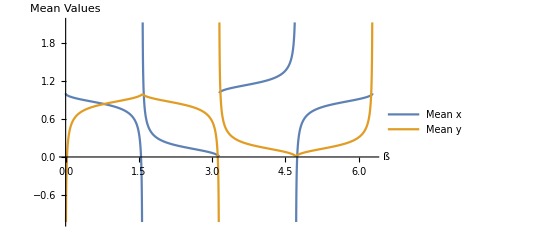

```mathematica
Plot[{{Meanx[ß,1/8],Meany[ß,1/8]}},{ß,0,2π},AxesLabel->{"ß","Mean Values"},PlotLegends->{"Mean x","Mean y"}]
```

## Plot of varx and vary, cov_xy as a function of ß

```mathematica
Varx[ß_,A_]:=Piecewise[{{A^2/12, ß==0||ß==2π}, {1/9 A Tan[ß], 0<ß&& ß<π/2}, {-2/3+A-A^2/4, ß==π/2}, {-1/9 A Tan[ß], π/2<ß&& ß<π}, {-1+A+A^2/12, ß==π}, {1/9 A Cot[ß], π<ß&& ß<(3π)/2}, {-2/3+A-A^2/4, ß==(3π)/2}, {-1/9 A Tan[ß], (3π)/2 <ß&& ß<2π}}]
Vary[ß_,A_]:=Piecewise[{{1/12, ß==0||ß==2π}, {1/9 A Cot[ß], 0<ß&& ß<π/2}, {1/12 (3-2 A)^2, ß==π/2}, {-1/9 A Cot[ß], π/2<ß&& ß<π}, {-1/4+A^2/3, ß==π}, {1/9 A Tan[ß], π<ß&& ß<(3π)/2}, {-1/4+A^2/3, ß==(3π)/2}, {-1/9 A Cot[ß], (3π)/2 <ß&& ß<2π}}]
Covxy[ß_,A_]:=Piecewise[{{0, ß==0||ß==2π}, {-A/18, 0<ß&& ß<π/2}, {0, ß==π/2}, {A/18, π/2<ß&& ß<π}, {0, ß==π}, {-A/18, (3π)/2 <ß&& ß<2π}, {0, ß==(3π)/2}, {A/18, (3π)/2 <ß&& ß<2π}}]
```

```mathematica
Covxy[(7π)/4,1/8]
```

-1/144

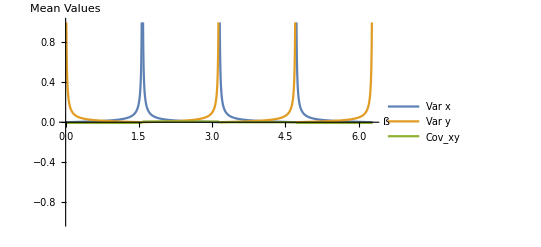

```mathematica
Plot[{Varx[ß,1/8],Vary[ß,1/8],Covxy[ß,1/8]},{ß,0,2π},AxesLabel->{"ß","Mean Values"},PlotLegends->{"Var x","Var y","Cov_xy"},PlotRange->{{0,2π},{-1,1}}]
```

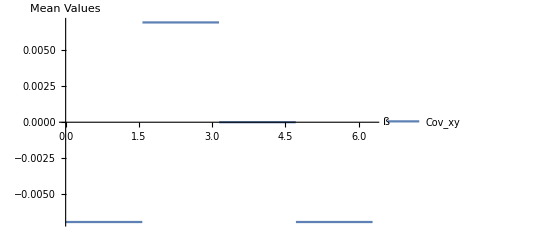

```mathematica
Plot[Covxy[ß,1/8],{ß,0,2π},AxesLabel->{"ß","Mean Values"},PlotLegends->{"Cov_xy"},PlotRange->{{0,2π},Automatic}]
```

## Plot of correlation as a function of ß

The correlation of x and y are always-A/(2 √(A Cot[ß]) √(A Tan[ß]))and A/(2 √(-A Cot[ß]) √(-A Tan[ß])) in different angle.Because  A >0,thus,

```mathematica
Corxy[ß_]:=Piecewise[{{0, ß==0||ß==2π}, {-1/2, 0<ß&&ß<π/2}, {0, ß==π/2}, {1/2, π/2<ß&&ß<π}, {0, ß==π}, {-1/2, (3π)/2 <ß&&ß<2π}, {0, ß==(3π)/2}, {1/2, (3π)/2 <ß&&ß<2π}}]
```

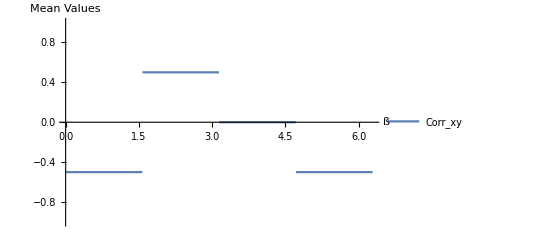

```mathematica
Plot[{Corxy[ß]},{ß,0,2π},AxesLabel->{"ß","Mean Values"},PlotLegends->{"Corr_xy"},PlotRange->{{0,2π},{-1,1}}]
```

## Manipulate Plot where you change θ and plot the triangular area with the robots, the mean, and a covariance ellipse.

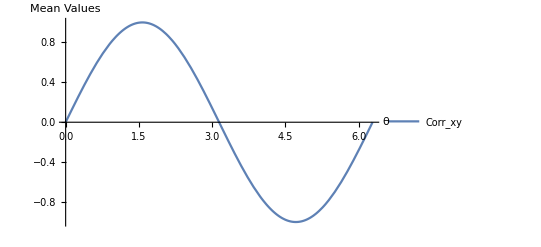

```mathematica
Plot[{Sin[θ]},{θ,0,2π},AxesLabel->{"θ","Mean Values"},PlotLegends->{"Corr_xy"}]
```

Trapezoid

## Plot of meanx and mean y as a function of ß

```mathematica
Meanx[ß_,A_]:=Piecewise[{{1-A/2, ß==0||ß==2π}, {(2-24 (-2+A) A-2 Sec[ß]^2)/(48 A), 0<ß&&ß<π/2}, {1/2, ß==π/2}, {(6 A+Cot[ß])/(12 A), π/2<ß&&ß<π}, {A/2, ß==π}, {1/2-Cot[ß]/(12 A), (3π)/2 <ß&&ß<2π}, {1/2, ß==(3π)/2}, {1/2-Cot[ß]/(12 A), (3π)/2 <ß&&ß<2π}}]

Meany[ß_,A_]:=Piecewise[{{1/2, ß==0||ß==2π}, {(6 A+Tan[ß])/(12 A), 0<ß&&ß<π/2}, {1-A/2, ß==π/2}, {1-A/2-Cot[ß]^2/(24 A), π/2<ß&&ß<π}, {1/2, ß==π}, {A/2+Cot[ß]^2/(24 A), (3π)/2 <ß&&ß<2π}, {A/2, ß==(3π)/2}, {A/2+Cot[ß]^2/(24 A), (3π)/2 <ß&&ß<2π}}]
```

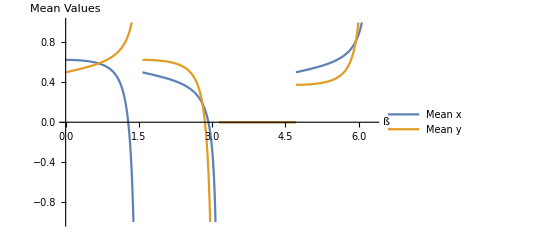

```mathematica
Plot[{Meanx[ß,3/4],Meany[ß,3/4]},{ß,0,2π},AxesLabel->{"ß","Mean Values"},PlotLegends->{"Mean x","Mean y"},PlotRange->{{0,2π},{-1,1}}]
```

## Plot of varx and vary, cov_xy as a function of ß

```mathematica
Varx[ß_,A_]:=Piecewise[{{A^2/12, ß==0||ß==2π}, {((3 (-1+8 A^2+48 A^4)+4 (1+48 A^4) Cos[2 ß]+(-1-24 A^2+48 A^4) Cos[4 ß]) Sec[ß]^4)/(4608 A^2), 0<ß&&ß<π/2}, {-2/3+A-A^2/4, ß==π/2}, {1/12-Cot[ß]^2/(144 A^2), π/2<ß&&ß<π}, {-1+A+A^2/12, ß==π}, {1/12-Cot[ß]^2/(144 A^2), π<ß&&ß<(3π)/2}, {-2/3+A-A^2/4, ß==(3π)/2}, {1/12-Cot[ß]^2/(144 A^2), (3π)/2 <ß&&ß<2π}}]
```

```mathematica
Vary[ß_,A_]:=Piecewise[{{1/12, ß==0}, {1/12-Tan[ß]^2/(144 A^2), 0<ß&&ß<π/2}, {1/12 (3-2 A)^2, ß==π/2}, {1/576 (48 A^2+24 Cot[ß]^2-Cot[ß]^4/A^2), π/2<ß&&ß<π}, {-1/4+A^2/3, ß==π}, {1/576 (48 A^2+24 Cot[ß]^2-Cot[ß]^4/A^2), π<ß&&ß<(3π)/2}, {-1/4+A^2/3, ß==(3π)/2}, {-(24 A (-2 A+Cot[ß])^3+(12 A^2+Cot[ß]^2)^2)/(576 A^2), (3π)/2 <ß&&ß<2π}}]
```

```mathematica
Covxy[ß_,A_]:=Piecewise[{{0, ß==0}, {-((-1+12 A^2+(1+12 A^2) Cos[2 ß]) Sec[ß]^2 Tan[ß])/(576 A^2), 0<ß&&ß<π/2}, {0, ß==π/2}, {((1-12 A^2+(1+12 A^2) Cos[2 ß]) Cot[ß] Csc[ß]^2)/(576 A^2), π/2<ß&&ß<π}, {0, ß==π}, {1/288 Cot[ß] (-12+Cot[ß]^2/A^2), (3π)/2 <ß&&<2π}, {0, ß==(3π)/2}, {1/288 Cot[ß] (-12+Cot[ß]^2/A^2), (3π)/2 <ß&&ß<2π}}]
```

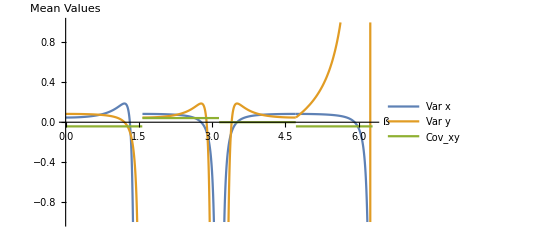

```mathematica
Plot[{Varx[ß,3/4],Vary[ß,3/4],Covxy[ß,3/4]},{ß,0,2π},AxesLabel->{"ß","Mean Values"},PlotLegends->{"Var x","Var y","Cov_xy"},PlotRange->{{0,2π},{-1,1}}]
```

## Plot of correlation as a function of ß

The correlation of x and y are always-A/(2 √(A Cot[ß]) √(A Tan[ß]))and A/(2 √(-A Cot[ß]) √(-A Tan[ß])) in different angle.Because  A >0,thus,

```mathematica
Corxy[ß_,A_]:=Piecewise[{{0, ß==0||ß==2π}, {-(√2 (-1+12 A^2+(1+12 A^2) Cos[2 ß]) Sec[ß]^2 Tan[ß])/(A^2 Abs[√(((-3+24 A^2+144 A^4+4 (1+48 A^4) Cos[2 ß]+(-1-24 A^2+48 A^4) Cos[4 ß]) Sec[ß]^4)/A^2) √(12-Tan[ß]^2/A^2)]), 0<ß&&ß<π/2}, {0, ß==π/2}, {((1-12 A^2+(1+12 A^2) Cos[2 ß]) Cot[ß] Csc[ß]^2)/(2 A^2 Abs[√(12-Cot[ß]^2/A^2) √(48 A^2+24 Cot[ß]^2-Cot[ß]^4/A^2)]), π/2<ß&&ß<π}, {0, ß==π}, {(-12 A^2 Cot[ß]+Cot[ß]^3)/(A^2 Abs[√(12-Cot[ß]^2/A^2) √(48 A^2+24 Cot[ß]^2-Cot[ß]^4/A^2)]), (3π)/2 <ß&&ß<2π}, {0, ß==(3π)/2}, {(-12 A^2 Cot[ß]+Cot[ß]^3)/(A^2 Abs[√(12-Cot[ß]^2/A^2) √(-(24 A (-2 A+Cot[ß])^3+(12 A^2+Cot[ß]^2)^2)/A^2)]), (3π)/2 <ß&&ß<2π}}]
```

```mathematica
Plot[{Corxy[ß]},{ß,0,2π},AxesLabel->{"ß","Mean Values"},PlotLegends->{"Corr_xy"},PlotRange->{{0,2π},{-1,1}}]
```

-Graphics-

## Manipulate Plot where you change θ and plot the triangular area with the robots, the mean, and a covariance ellipse.

```mathematica
Plot[{Sin[θ]},{θ,0,2π},AxesLabel->{"θ","Mean Values"},PlotLegends->{"Corr_xy"}]
```

-Graphics-